# Graphs of continuous functions

This Mathematica notebook is licensed under a  .

It provides examples of graphs of continuous functions in one or more variables.

The notebook is still rough and incomplete.  It will be revised from time to time.  I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

Charles Wells

Continuous functions of one variable

## ContFunc

```mathematica
2-(1.8)^2
```

-1.24

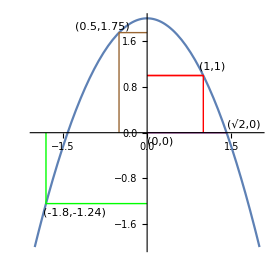

```mathematica
Show[Plot[2-x^2,{x,-2,2}],Graphics[{Red,Line[{{0,1},{1,1},{1,0}}],Line[{{0,1},{1,1}}],Brown,Line[{{-.5,0},{-.5,1.75},{0,1.75}}],Green,Line[{{-1.8,0},{-1.8,2-(1.8)^2},{0,2-(1.8)^2}}],
Thick,Purple,Line[{{Sqrt[2],0},{0,0}}],
Black,Inset["(1,1)",{1+.15,1+.15}],Inset["(0.5,1.75)",{-.5+-.3,1.75+.1}],Inset["(-1.8,-1.24)",{2-(1.8)^2-.05,2-(1.8)^2-.15}],Inset["(√2,0)",{Sqrt[2]+.3,.15}],Inset["(0,0)",{.24,-.15}]}
],AspectRatio->1,ImageSize->275
]
```

```mathematica
uppar[t_]:=2-t^2
```

```mathematica
Manipulate[
Show[
Plot[uppar[x],{x,-2,2}],
Graphics[{Red,Line[{{t,0},{t,uppar[t]},{0,uppar[t]}}]}
],
AspectRatio->1,ImageSize->175
],{t,-2,2}]
```

```mathematica
upparmovie=Table[Show[
Plot[uppar[x],{x,-2,2}],
Graphics[{Red,Line[{{t,0},{t,uppar[t]},{0,uppar[t]}}]}
],
AspectRatio->1,ImageSize->175
],{t,-2,2,.1}];
```

```mathematica
Export["Z:\\www\\MM\\Mathematica\\Function Representations\\upparmovie.gif",upparmovie]
```

### ContFunc2

```mathematica
foolyou[x_]:=.0002((x^3-10)/(3 Exp[-x]+1))^6
```

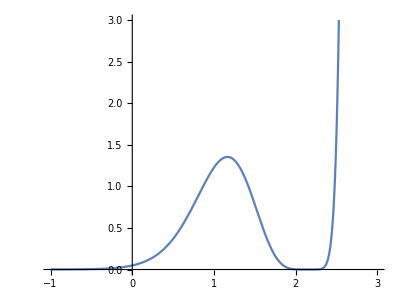

```mathematica
Plot[foolyou[x],{x,-1,3},PlotRange->{{-1,3},{0,3}},AspectRatio->3/4]
```

```mathematica
10^(1/3)//N
```

2.15443

```mathematica
Solve[x^3-10==0,x]
```

Solve::ivar: 0.999942 is not a valid variable.

Solve[False,0.999942]

```mathematica
-(-10)^(1/3)//N
```

-1.07722-1.8658 ⅈ

```mathematica
(-1)^(2/3) 10^(1/3)//N
```

-1.07722+1.8658 ⅈ

```mathematica
foolyou'[x]
```

1.40809

```mathematica
foolyou''[x]
```

-5.94097

```mathematica
NSolve[foolyou'[x]==0,x,Reals]
```

NSolve::ivar: 0.999942 is not a valid variable.

NSolve[False,0.999942,Reals]

```mathematica
foolyou''[1.1648251336938016]
```

-10.6664

## Discontinuous function

```mathematica
Remove[dfunc]
```

```mathematica
dfunc[x_]:=2-x^2/;x>0;dfunc[x_]:=2-x^2/;x<-1;dfunc[x_]:=1-x^2/;x>-1&&x<0;
```

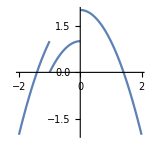

```mathematica
Plot[dfunc[x],{x,-2,2},AspectRatio->1,Exclusions->{x=0,x=-1 },ImageSize->150]
```

Polar Plot

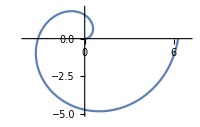

```mathematica
PolarPlot[t,{t,0,2Pi},ImageSize->200,PlotRange->{{-4,7},{-5,2}},AspectRatio->7/11]
```

```mathematica
ToPolarCoordinates[{t,1}]
```

{√(1+t^2),ArcTan[t,1]}

```mathematica
FromPolarCoordinates[{√(1+t^2),ArcTan[t,1]}]
```

{t,1}

```mathematica
ToPolarCoordinates[{x,y}]
```

{1.00023,-3.12003}

```mathematica
FromPolarCoordinates[{r,t}]
```

{r Cos[t],r Sin[t]}

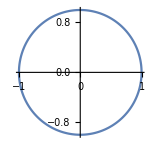

```mathematica
PolarPlot[1,{t,0,2Pi},ImageSize->150]
```

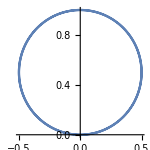

```mathematica
PolarPlot[Sin[t],{t,0,2Pi},ImageSize->150]
```

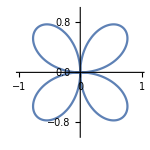

```mathematica
PolarPlot[Sin[2t],{t,0,2Pi},PlotRange->{{-1,1},{-1,1}},ImageSize->150]
```

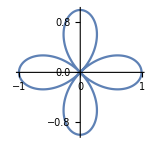

```mathematica
PolarPlot[Cos[2t],{t,0,2Pi},ImageSize->150]
```

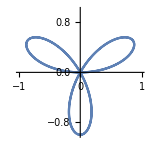

```mathematica
PolarPlot[Sin[3t],{t,0,2Pi},PlotRange->{{-1,1},{-1,1}},ImageSize->150]
```

Functions from R to R x R

## Unit Circle

### Bare unit circle

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},ImageSize->150]
```

-Graphics-

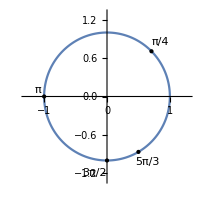

```mathematica
Show[{ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotRange->{-1.3,1.3},ImageSize->200],Graphics[{PointSize[Large],Black,Point[{Cos[5 Pi/3],Sin[5 Pi/3]}],Text["5π/3",{Cos[5Pi/3]+.15,Sin[5 Pi/3]-.15}],Point[{Cos[-Pi/2],Sin[-Pi/2]}],Text["3π/2",{Cos[3Pi/2]-.2,Sin[3Pi/2]-.2}],Point[{Cos[Pi],Sin[Pi]}],Text["π",{Cos[Pi]-.1,Sin[Pi]+.1}],Point[{Cos[Pi/4],Sin[Pi/4]}],Text["π/4",{Cos[Pi/4]+.15,Sin[Pi/4]+.15}]}]}]
```

```mathematica
Sqrt[3]/2//N
```

0.866025

```mathematica
Manipulate[
Show[ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotRange->{-1.3,1.3},ImageSize->200],Graphics[{PointSize[Large],Black,Point[{Cos[t],Sin[t]}]}],ImageSize->150],{{t,0},0,10 Pi}]
```

```mathematica
Animate[
Show[
ParametricPlot[{Cos[t],Sin[t]},{t,0,8Pi},PlotRange->{{-1.3,2.3},{-1.3,1.3}},ImageSize->200],Graphics[{PointSize[Large],Black,Point[{Cos[t],Sin[t]}],Text[t,{2,.5}]}],ImageSize->150],{{t,0},0,10 Pi},AnimationRunning->False]
```

```mathematica
outstring[t_]:=StringJoin["t=",ToString[NumberForm[N[(t/Pi)],{3,3}]],"π"]
```

```mathematica
outstring[1.3]
```

t=0.414π

```mathematica
Table[Show[
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotRange->{{-1.3,2.5},{-1.3,1.3}},ImageSize->200],Graphics[{PointSize[Large],Black,Point[{Cos[t],Sin[t]}],Text[NumberForm["t="N[(t/Pi)],{3,3}]"π",{2,.5}]}],ImageSize->250,Axes->False],{t,0,2Pi,Pi/30}];
```

```mathematica
circlemovie=Table[Show[
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotRange->{{-1.3,2.5},{-1.3,1.3}},ImageSize->200],Graphics[{PointSize[Large],Black,Point[{Cos[t],Sin[t]}],Text[outstring[t],{2,.5}]}],ImageSize->250,Axes->False],{t,0,2Pi,Pi/30}];
```

```mathematica
ListAnimate[circlemovie, AnimationRunTime->1,AnimationRunning->False]
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\circlemovie.gif",circlemovie]
```

## Unit circle with universal cover

```mathematica
ParametricPlot3D[{{Cos[t],Sin[t],0},{Cos[t],Sin[t],.2t}},{t,0,10Pi},ImageSize->200]
```

-Graphics3D-

### Show fibers

```mathematica
Show[ParametricPlot3D[{{Cos[t],Sin[t],0},{Cos[t],Sin[t],.2t}},{t,0,8Pi}],Graphics3D[{PointSize[Large],Black,Point[{Cos[5 Pi/3],Sin[5 Pi/3],0}],Point[{Cos[3 Pi/2],Sin[3 Pi/2],0}],Point[{Cos[Pi],Sin[Pi],0}],Point[{Cos[Pi/4],Sin[Pi/4],0}],Point[{Cos[5 Pi/3],Sin[5 Pi/3],.2 (5Pi/3)}],Point[{Cos[3 Pi/2],Sin[3 Pi/2],.2 (3 Pi/2)}],Point[{Cos[Pi],Sin[Pi],.2  Pi}],Point[{Cos[Pi/4],Sin[Pi/4],.2(Pi/4)}],Point[{Cos[5 Pi/3],Sin[5 Pi/3],.2(5 Pi/3+2 Pi)}],Point[{Cos[3 Pi/2],Sin[3 Pi/2],.2(3 Pi/2+2 Pi)}],Point[{Cos[Pi],Sin[Pi],.2 (Pi+2 Pi)}],Point[{Cos[Pi/4],Sin[Pi/4],.2(Pi/4+2 Pi)}],Point[{Cos[5 Pi/3],Sin[5 Pi/3],.2(5 Pi/3+4Pi)}],Point[{Cos[3 Pi/2],Sin[3 Pi/2],.2(3 Pi/2+4 Pi)}],Point[{Cos[Pi],Sin[Pi],.2(Pi+4 Pi)}],Point[{Cos[Pi/4],Sin[Pi/4],.2(Pi/4+4 Pi)}],Point[{Cos[5 Pi/3],Sin[5 Pi/3],.2(5 Pi/3+6Pi)}],Point[{Cos[3 Pi/2],Sin[3 Pi/2],.2(3 Pi/2+6 Pi)}],Point[{Cos[Pi],Sin[Pi],.2(Pi+6 Pi)}],Point[{Cos[Pi/4],Sin[Pi/4],.2(Pi/4+6 Pi)}]
}],Boxed->True
]
```

-Graphics3D-

```mathematica
Manipulate[Show[ParametricPlot3D[{{Cos[t],Sin[t],0},{Cos[t],Sin[t],.2t}},{t,0,10Pi},ImageSize->170],Graphics3D[{PointSize[Large],Black,Point[{Cos[t],Sin[t],0}],Point[{Cos[t],Sin[t],.2t}]
}]
],{t,0,10 Pi}]
```

```mathematica
covermovie=Table[Show[
ParametricPlot3D[{{Cos[t],Sin[t],0},{Cos[t],Sin[t],.2t}},{t,0,8Pi},Axes->False],Graphics3D[{PointSize[Large],Black,Point[{Cos[t],Sin[t],0}],Point[{Cos[t],Sin[t],.2t}],Text[outstring[t],{2,.5,1}]}],ImageSize->250],{t,0,8Pi,Pi/30}];
```

```mathematica
ListAnimate[covermovie, AnimationRunTime->1,AnimationRunning->False]
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\covermovie.gif",covermovie]
```

Spiral

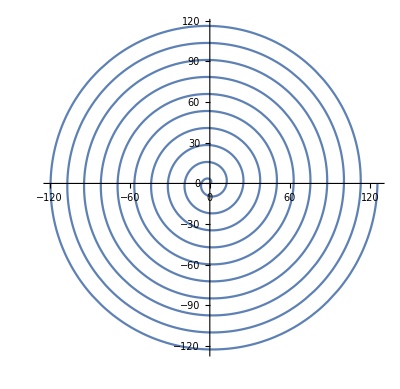

```mathematica
ParametricPlot[{2 t Cos[t],2 t Sin[t]},{t,0,20 Pi}]
```

## Spiral with universal cover

```mathematica
ParametricPlot3D[{2 t Cos[t],2 t Sin[t],8t},{t,0,20 Pi},ImageSize->200]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{2 t Cos[t],2 t Sin[t],0},{2 t Cos[t],2 t Sin[t],8t}},{t,0,20 Pi},ImageSize->200]
```

-Graphics3D-

Figure eight

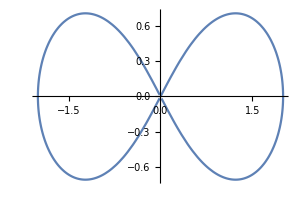

```mathematica
PolarPlot[Sqrt[4Cos[2t]],{t,0,2 Pi},ImageSize->300]
```

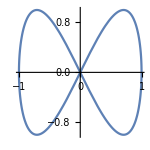

```mathematica
ParametricPlot[{x=Cos[t],y=Sin[2t]},{t,0,2Pi},ImageSize->150]
```

## Figure 8 with universal cover

```mathematica
ParametricPlot3D[{{x=Cos[t],y=Sin[2t],0},{x=Cos[t],y=Sin[2t],.1t}},{t,0,10Pi},ImageSize->250,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Manipulate[
ParametricPlot3D[{{x=Cos[t],y=Sin[2t],0},{x=Cos[t],y=Sin[2t],.1t}},{t,0,10Pi},ImageSize->150,AxesLabel->{X,Y,Z},ViewPoint->{a,b,c}],{{a,-1},-5,5},{{b,4.3},-5,5},{{c,1.92},-5,5}]
```

```mathematica
covermovie=Table[Show[
ParametricPlot3D[{{Cos[t],Sin[t],0},{Cos[t],Sin[t],.2t}},{t,0,8Pi},Axes->False],Graphics3D[{PointSize[Large],Black,Point[{Cos[t],Sin[t],0}],Point[{Cos[t],Sin[t],.2t}],Text[outstring[t],{2,.5,1}]}],ImageSize->250],{t,0,8Pi,Pi/30}];
```

```mathematica
Fig8movie=Table[Show[
ParametricPlot3D[{{Cos[t],Sin[2t],0},{Cos[t],Sin[2t],.1t}},{t,0,8Pi},AxesLabel->{X,Y,Z},ViewPoint->{-2.65,-5,1.12}],Graphics3D[{PointSize[Large],Black,Point[{Cos[t],Sin[2t],0}],Point[{Cos[t],Sin[2t],.1t}]}],ImageSize->250],{t,0,8Pi,Pi/30}];
```

```mathematica
ListAnimate[Fig8movie, AnimationRunTime->3,AnimationRunning->True]
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\covermovie.gif",covermovie]
```

```mathematica
Export["C:\\Users\\C&J\\Desktop\\Fig8movie.gif",Fig8movie]
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\Fig8movie.gif",Fig8movie]
```

3 D Curves

```mathematica
ParametricPlot3D[{Cos[t],Sin[2t],Log[t]},{t,1,20Pi},ImageSize->250,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x=Cos[t],y=Sin[t],z=Sin[7t]},{t,0,10Pi},ImageSize->250,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
crownmovie=Table[Show[
ParametricPlot3D[{{Cos[t],Sin[t],Sin[7t]}},{t,0,2Pi},Axes->False],Graphics3D[{PointSize[Large],Black,Point[{Cos[t],Sin[t],Sin[7t]}]}],ImageSize->250],{t,0,2Pi,Pi/60}];
```

```mathematica
Export["W:\\www\\MM\\Mathematica\\Function Representations\\crownmovie.gif",crownmovie]
```

Curve in space

```mathematica
shift[t_]:=(-4t^2+53t)/18
```

```mathematica
{shift'[t],shift''[t]}
```

{1/18 (53-8 t),-4/9}

```mathematica
{shift[0],shift[10]}//N
```

{0.,7.22222}

```mathematica
ParametricPlot3D[{shift[t],t,.4(-t^2+10t)},{t,0,10},PlotRange->{{-2,10},{0,10},{0,10}},AxesLabel->{"x","y","z"},ImageSize->300,ViewPoint->{0,-8,0}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{shift[t],t,.4(-t^2+10t)},{0,t,.4(-t^2+10t)},{shift[t],t,0}},{t,0,10},PlotRange->{{-2,10},{0,10},{0,10}},AxesLabel->{"x","y","z"},ImageSize->250]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{shift[t],t,.4(-t^2+10t)},{0,t,.4(-t^2+10t)},{shift[t],t,0}},{t,0,10},PlotRange->{{0,10},{0,10},{0,10}},ImageSize->250]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{shift[t],t,.4(-t^2+10t)},{0,t,.4(-t^2+10t)},{shift[t],t,0}},{t,0,10},PlotRange->{{-1,10},{0,10},{0,10}},ImageSize->250,AxesLabel->{"x","y","z"},ViewPoint->{0,-6,0}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{shift[t],t,.4(-t^2+10t)},{0,t,.4(-t^2+10t)},{shift[t],t,0}},{t,0,10},PlotRange->{{-0,10},{0,10},{0,10}},ImageSize->250,AxesLabel->{"x","y","z"},ViewPoint->{0,0,-6}]
```

-Graphics3D-

### Variation

```mathematica
ParametricPlot3D[{{shift[t],t+Sin[5t],.4(-t^2+10t)},{0,t,.4(-t^2+10t)},{shift[t],t,0}},{t,0,10},PlotRange->{{-2,11},{-1,11},{-1,11}},ImageSize->250]
```

-Graphics3D-

Experiment 2

```mathematica
exp2a[t_]:=3.3(t^3-t)+t
```

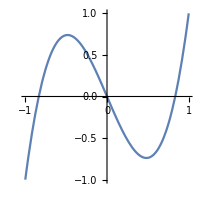

```mathematica
Plot[exp2a[t],{t,-1,1},ImageSize->200,PlotRange->{{-1,1},{-1,1}},AspectRatio->1]
```

```mathematica
exp2b[t_]=-(-1.6(t-1)(t+.3)(t+1))+t
```

t+1.6 (-1+t) (0.3+t) (1+t)

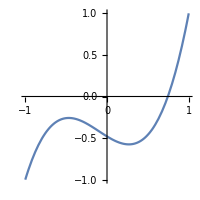

```mathematica
Plot[exp2b[t],{t,-1,1},ImageSize->200,PlotRange->{{-1,1},{-1,1}},AspectRatio->1]
```

```mathematica
InterpolatingPolynomial[{{-1,-1},{0,1},{1,-1}},t]
```

-1+(2-2 t) (1+t)

```mathematica
exp2c[t_]:=InterpolatingPolynomial[{{-1,-1},{-.5,-.5},{0,-.4},{.3,.5},{.6,.4},{1,1}},t]
```

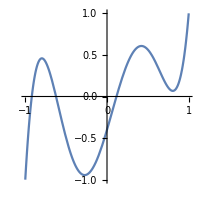

```mathematica
Plot[exp2c[t],{t,-1,1},ImageSize->200,PlotRange->{{-1,1},{-1,1}},AspectRatio->1]
```

```mathematica
axst[t_]:=Style[t,14,Bold]
```

```mathematica
ParametricPlot3D[{{exp2a[t],exp2b[t],exp2c[t]},
{1,t,exp2a[t]}},{t,-1,1},
ImageSize->250,PlotRange->{{-1,1},{-1,1},{-1,1}},AxesLabel->{"x","y","z"},LabelStyle->Directive[Black,Bold],ViewPoint->{5,0,0},Ticks->{{-1,0,1},{-1,0,1},{-1,0,1}}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{exp2a[t],exp2b[t],exp2c[t]},
{exp2a[t],-1,t},{t,exp2b[t],-1},{-1,t,exp2c[t]}},{t,-1,1},
ImageSize->250,PlotRange->{{-1,1},{-1,1},{-1,1}},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{exp2a[t],exp2b[t],exp2c[t]},
{exp2a[t],-1,-1}},
{t,-1,1},ImageSize->250,PlotRange->{{-1,1},{-1,1},{-1,1}},AxesLabel->{axst["x"],axst["y"],axst["z"]}
]
```

-Graphics3D-

```mathematica
Manipulate[
ParametricPlot3D[{{exp2a[t],exp2b[t],exp2c[t]}},
{t,-1,1},ImageSize->250,PlotRange->{{-1,1},{-1,1},{-1,1}},AxesLabel->{"x","y","z"},ViewPoint->{a,b,c}],
{{a,Pi},1,50},{{b,Pi/2},1,50},{{c,2},1,50}]
```